The black points are the original data points. The pink points are on the curve and they are setted by the parameters, ti. The red points are also on the curve and they are set by knots. They seperate the curve to L segment. The gray lines link the control points after iteration. The blue lines link the final control points. The magenta curve shows the curve after first iteration and the green curve is the final curve.

{0.,0.024151,0.0478249,0.0647543,0.0768843,0.0780851,0.0840741,0.0918905,0.111141,0.126566,0.153002,0.170077,0.188351,0.203544,0.217186,0.219988,0.222473,0.232118,0.250129,0.264916,0.287226,0.309462,0.321643,0.336841,0.346293,0.347221,0.348261,0.359279,0.375366,0.38873,0.410729,0.42888,0.441126,0.451783,0.457571,0.465834,0.475735,0.482626,0.490602,0.505077,0.520444,0.541017,0.556787,0.566162,0.568607,0.571933,0.572902,0.580767,0.590012,0.607001,0.623301,0.634306,0.644656,0.6599,0.664565,0.665683,0.668262,0.674922,0.685837,0.695779,0.706253,0.723713,0.729893,0.73965,0.74816,0.749542,0.750536,0.761372,0.766769,0.78137,0.791647,0.801906,0.811566,0.818131,0.821603,0.829609,0.833839,0.83938,0.848993,0.855098,0.871442,0.87819,0.891399,0.894134,0.898708,0.902926,0.904604,0.907161,0.920907,0.929839,0.936797,0.942647,0.953106,0.959173,0.96931,0.975089,0.975863,0.97797,0.983349,0.990746,1.}

{0,0,0,0,1/15,2/15,1/5,4/15,1/3,2/5,7/15,8/15,3/5,2/3,11/15,4/5,13/15,14/15,1,1,1,1}

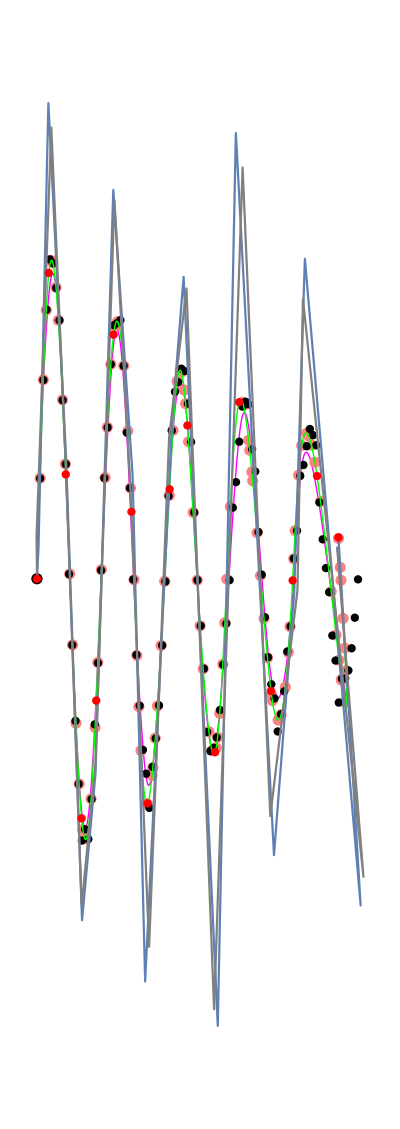

| Max | Min | Ave
1st iter err | 0.194396 | 0.00359005 | 0.0695985
Last iter err | 0.05342 | 0.000253378 | 0.0102146

| Max | Min | Ave
1st iter ang | 3.13842 | 0.000470938 | 1.60202
Last iter ang | 3.13844 | 0.0947562 | 1.52662

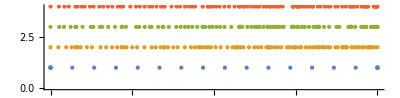

```mathematica
(*data4 contaions 100 points. I didn't add it to manipulate since it is too slow. I show it in another file.*)
data1=Table[{Cos[x]//N, Sin[x]//N},{x,0,6}];
data2=Table[{x, Sin[x]//N},{x,0,12}];
data3=Table[{x,x},{x,1,10}];
data4=Table[{i,Exp[-i]Sin[10Pi i]+RandomReal[.1]},{i,0,1,.01}];

(*d is degree,which is three,n is # of control point*)

l=15;
iter=6;


(*chord length parameter*)
(*calculate the distance for parameter*)
dist[pts_]:=Accumulate[Table[EuclideanDistance[pts[[i]],pts[[i+1]]],{i,Length[pts]-1}]];
(*set ti from 0 to 1 by using Chord length*)
uparam[pts_]:=N[Prepend[dist[pts]/Last[dist[pts]],0]];

(*I used the two function to calculate the knots first. The result is almost the same, so I used uniformed knots.*)
(*set ti for different control points*)
ctrlparam[n_,pts_,param_]:=Join[Table[0,{i,0,0}],Table[Sum[param[[i]],{i,j,Length[pts]-n+j}]/(Length[pts]-n+1),{j,2,n-1}],Table[1,{i,0,0}]];
(*set knot for different degree*)
kfun[d_,ctrlparam_]:=Join[Table[0,{i,0,d}],Table[Sum[ctrlparam[[i]],{i,j,j+d-1}]/d,{j,2,Length[ctrlparam]-d}], Table[1,{i,0,d}]];

knotfun[l_,uparam_]:=Join[Table[0,{i,0,3}],Table[(uparam[[Ceiling[i*Length[uparam]/l]]]+uparam[[Floor[i*Length[uparam]/l]]])/2,{i,1,l-1}],Table[1,{i,0,3}]];
(*calculate the basis*)
(*Built the matrix M for least square*)
mbasis[uparam_,n_,d_,knot_]:=With[{param=uparam},Table[BSplineBasis[{d,knot},j-1,param[[i]]],{i,Length[param]},{j,n}]];
curve[pts_,knot_,n_,d_,t_]:=Sum[BSplineBasis[{d,knot},i,t]*pts[[i+1]],{i,0,(Length[pts]-1)}];



Print[Style["The black points are the original data points. The pink points are on the curve and they are setted by the parameters, ti. The red points are also on the curve and they are set by knots. They seperate the curve to L segment. The gray lines link the control points after iteration. The blue lines link the final control points. The magenta curve shows the curve after first iteration and the green curve is the final curve.",18,Red]];
pts=data4;

n=l+3;
d=3;

(*Original parameter.*)
param=uparam[pts]
(*(*For different amount of control points, set different parameter.*)
ctrlparameter=ctrlparam[n,pts,param];*)
(*The knots for different degree*)

knot=Join[ConstantArray[0,d],Range[0,1,1/(n-d)],ConstantArray[1,d]]
(*knot=knotfun[l,param]*)
(*The control point*)
ctrlpts=LeastSquares[mbasis[param,n,d,knot],pts];
mbasis[param,n,d,knot];

crtparam=param;
(*crtctrlparameter=ctrlparameter;*)
crtknot=knot;
crtctrlpts=ctrlpts;
(*use this funtion to get the vector on curve*)
divcurve[t_]:=curve[crtctrlpts,crtknot,n,d,t];

(*The length of the curve.*)
curvelength=ArcLength[curve[crtctrlpts,crtknot,n,d,t],{t,crtknot[[d+1]],knot[[Length[crtknot]-d]]}];

(*error represent the distance between original data points with the points on the curve which set by parameter ti.*)
error=Table[0,{j,1,Length[pts]}];
(*The vector at ti on the curve*)
tengentvec=Table[{0,0},{j,1,Length[pts]}];
(*The vecter from points on curve to data points*)
errvec=Table[{0,0},{j,1,Length[pts]}];
(*The angle between two vecter*)
vecang=Table[0,{j,1,Length[pts]}];
(*The length used to change ti*)
lengthl=Table[0,{j,1,Length[pts]}];
error1=error;
vecang1=vecang;
crtctrlpts1=crtctrlpts;

Do[(
Do[
error[[j]]=EuclideanDistance[curve[crtctrlpts,crtknot,n,d,crtparam[[j]]],pts[[j]]];
tengentvec[[j]]=divcurve'[crtparam[[j]]];
errvec[[j]]=pts[[j]]-curve[crtctrlpts,crtknot,n,d,crtparam[[j]]];
If[error[[j]]==0,vecang[[j]]=0,vecang[[j]]=VectorAngle[tengentvec[[j]],errvec[[j]]]];
lengthl[[j]]=error[[j]]*Cos[vecang[[j]]];
(*Parameter correction. If the length of new vector is less than the original vector, do the correction, else the ti will be corrected by half of the length.*)
tmplengthl=lengthl[[j]];
tmpparam=crtparam[[j]];
If[crtparam[[j]]+tmplengthl>1,tmpparam=1,If[crtparam[[j]]+tmplengthl<0,tmpparam=0,tmpparam=crtparam[[j]]+tmplengthl;]];
While[EuclideanDistance[curve[crtctrlpts,crtknot,n,d,tmpparam],pts[[j]]]>error[[j]]&&tmplengthl≠0,(tmplengthl=tmplengthl/2;If[crtparam[[j]]+tmplengthl>1,tmpparam=1,If[crtparam[[j]]+tmplengthl<0,tmpparam=0,tmpparam=crtparam[[j]]+tmplengthl;]];)];
If[tmpparam<0,crtparam[[j]]=0,If[tmpparam>1,crtparam[[j]]=1,crtparam[[j]]=tmpparam;]];
,{j,1,Length[pts]}];
(*Here is the control points after correction*)
crtctrlpts=LeastSquares[mbasis[crtparam,n,d,crtknot],pts];
(*store the data after first iteration*)
If[k==1,
(error1=error;
vecang1=vecang;
crtctrlpts1=crtctrlpts;
crtparam1=crtparam;)];

)
,{k,1,iter}];

(*get the max, min, mean error and angle*)
errmax1=Max[error1];
errmin1=Min[error1];
errave1=Mean[error1];
errmax=Max[error];
errmin=Min[error];
errave=Mean[error];
angmax1=Max[vecang1];
angmin1=Min[vecang1];
angave1=Mean[vecang1];
angmax=Max[vecang];
angmin=Min[vecang];
angave=Mean[vecang];

(*Output the curves, points and polygon*)
datapts=Graphics[{Black,PointSize[0.015],Point[pts],PointSize[0.02],Point[pts[[1]]]}];
jpts = Table[curve[crtctrlpts,crtknot,n,d,crtknot[[i]]], {i,d+1,Length[crtknot]- d,1}];
jptsplot = Graphics[{Red,PointSize[0.015],Point[jpts]}];
parpts=Table[curve[crtctrlpts,crtknot,n,d,crtparam[[j]]],{j,1,Length[pts]}];
parptsplot=Graphics[{Pink,PointSize[0.02],Point[parpts]}];
ctrlpoints=Graphics[{Green,PointSize[0.015],Point[crtctrlpts],PointSize[0.02],Point[crtctrlpts[[1]]]}];
cplot=ParametricPlot[curve[crtctrlpts,crtknot,n,d,t],{t,crtknot[[d+1]],crtknot[[Length[crtknot]-d]]},PlotStyle->{Thick,Green}];
cplot1=ParametricPlot[curve[crtctrlpts1,crtknot,n,d,t],{t,crtknot[[d+1]],crtknot[[Length[crtknot]-d]]},PlotStyle->{Thick,Magenta}];
ddplot=ListLinePlot[crtctrlpts];
ddplot1=ListLinePlot[crtctrlpts1,PlotStyle->Gray];

Show[{cplot1,parptsplot,datapts,cplot,ddplot,ddplot1,jptsplot},Axes->False,PlotRange->All,ImageSize->400]
TableForm[{{errmax1,errmin1,errave1},{errmax,errmin,errave}},TableHeadings->{{"1st iter err","Last iter err"},{"Max","Min","Ave"}},TableDirections->Column]
TableForm[{{angmax1,angmin1,angave1},{angmax,angmin,angave}},TableHeadings->{{"1st iter ang","Last iter ang"},{"Max","Min","Ave"}},TableDirections->Column]
NumberLinePlot[{crtknot,param,crtparam1,crtparam}]
```